## Universal Gates

### Bools and Matrix

Conversions from Bools to Integers

```mathematica
b2i[b_]:=If[b, 1, 0];
b2i[b_List]:=b2i/@b

b2v[b_Boole]:=If[b, {0, 1}, {1, 0}]
b2v[b_Integer]:=If[b==1, {0, 1}, {1, 0}]
v2b[{v1_, v2_}]:=If[{v1,v2}=={0, 1}, 1, 0]
```

### Tensors

```mathematica
tensor[v__] := Flatten[TensorProduct[v]]
```

Tensor Example

```mathematica
tensor[{0, 1}, {1, 0}, {0, 1}]
KroneckerProduct[Array[Subscript[a, ##]&, {2, 2}], Array[Subscript[b, ##]&, {2, 2}]]//MatrixForm
```

{0,0,0,0,0,1,0,0}

(a_(1,1) b_(1,1) | a_(1,1) b_(1,2) | a_(1,2) b_(1,1) | a_(1,2) b_(1,2)
a_(1,1) b_(2,1) | a_(1,1) b_(2,2) | a_(1,2) b_(2,1) | a_(1,2) b_(2,2)
a_(2,1) b_(1,1) | a_(2,1) b_(1,2) | a_(2,2) b_(1,1) | a_(2,2) b_(1,2)
a_(2,1) b_(2,1) | a_(2,1) b_(2,2) | a_(2,2) b_(2,1) | a_(2,2) b_(2,2))

### Matrix Definitions

Non-Adjacent Matrices

```mathematica
(* SWAP *)
Vi1[i_, n_, s1_, s2_]:=Module[{bv, sbv},
bv=IntegerDigits[i, 2, n];
sbv=tensor@@(b2v/@Table[bv[[Switch[j, s1, s2, s2, s1, _, j]]], {j,n}])]
matrixSwap[n_, s1_, s2_]:=Vi1[#, n, s1, s2]&/@Range[0, 2^n-1]
```

```mathematica
(* RETURN *)
Vi2[i_, n_, s1_, s2_]:=tensor@@b2v/@(IntegerDigits[i, 2, n])[[s1;;s2]]
matrixReturn[n_, s1_, s2_]:=Transpose[Vi2[#, n, s1, s2]&/@Range[0, 2^n-1]]
```

```mathematica
(* EXPAND *)
matrixZeroExpand[n_, s1_, s2_]:=Module[{ω, ξ, Ω, Ξ},
 ω=s1-1; Ω=2^ω;
 ξ=s2; Ξ=2^ξ;
 Table[Module[{Vω, Vξ, VΞ},
  Vω=IntegerDigits[i, 2, ω];
  Vξ=Join[Vω, ConstantArray[0, ξ-ω]];
  VΞ=fullState[Vξ];
  VΞ], {i, 0, Ω-1}]]//Transpose

matrixRepeatExpand[n_, s1_, s2_]:=Module[{ω, ξ, Ω, Ξ},
 ω=s1-1; Ω=2^ω;
 ξ=s2; Ξ=2^ξ;
 Table[Module[{Vω, Vξ, VΞ},
  Vω=IntegerDigits[i, 2, ω];
  Vξ=Flatten[ConstantArray[Vω, ⌈ξ/ω⌉]][[;;ξ]];
  VΞ=fullState[Vξ];
  VΞ], {i, 0, Ω-1}]]//Transpose
```

Fixed Matrices

```mathematica
I2={{1, 0}, {0, 1}};
matrixNOT={{0, 1}, {1, 0}};

matrixCopy={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}};
matrixNand={{0, 0, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}};
matrixNor={{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 1}, {0, 0, 0, 0}};
```

```mathematica
matrixSwap[2, 1, 2]
```

{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}

## Matrix Gate Application

### Matrix for Single Column

```mathematica
(* For[i=1,i<=Length[gates],i++,Module[ *)
matrixFormOfColumn[G_, n_]:=
 Module[{s1, s2, M},
 s1=G[[1, 1]];
 s2=G[[1,2]];
 M=G[[2]];

(* Switch for irregular functions *)
 Switch[M,
  matrixSwap, matrixSwap[n, s1, s2],
  matrixReturn, matrixReturn[n, s1, s2],
  matrixExpand, matrixExpand[s1-1, s1, s2],
  _, Module[{N1, N2, N3, IN1, IN2, IN3},
   N1=s1-1;
   N2=s2-s1+1;
   N3=n-s2;
   IN1=ConstantArray[I2, N1];
   IN2={M};
   IN3=ConstantArray[I2, N3];
   KroneckerProduct@@Join[IN1, IN2, IN3]
  ]
 ]
]
```

### Full Circuit Operator

```mathematica
initialStateConstructionZeros[a_, b_, n_]:=tensor@@b2v/@Join[{a, b}, ConstantArray[0, n - 2]]
initialStateConstructionRepeating[a_, b_, n_]:=tensor@@b2v/@Flatten[ConstantArray[{a, b}, n/2]]
circuitGatesFunction[gates_, n_, initialStateConstructionMethod_: initialStateConstructionZeros]:=Function[{a,b},
 Module[{currentStateVector},
  currentStateVector=initialStateConstructionMethod[a, b, n];
  For[i=1,i<=Length[gates],i++,
   currentStateVector=matrixFormOfColumn[gates[[i]], n].currentStateVector;
  ];
  currentStateVector
 ]
]
```

### XOR Gate from NAND Example Circuit

```mathematica
gates={
{{3, 5}, matrixExpand},
{{2, 3},matrixCopy},
{{2, 3},matrixNand},
{{1, 2},matrixSwap},
{{3, 4},matrixSwap},
{{2, 3},matrixCopy},
{{2, 3},matrixNand},
{{1, 2},matrixNand},
{{3, 4},matrixNand},
{{2, 3},matrixSwap},
{{3, 4},matrixNand},
{{4, 5},matrixCopy},
{{4, 5},matrixNand},
{{5, 5},matrixReturn}
};

xorFromNandMatrix=circuitGatesFunction[gates, 5, initialStateConstructionZeros];

v2b/@
{xorFromNandMatrix[0, 0],
xorFromNandMatrix[0, 1],
xorFromNandMatrix[1, 0],
xorFromNandMatrix[1, 1]}
```

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«22»},{0,1,0,0,0,0,0,0,0,0,«22»},{0,0,1,0,0,0,0,0,0,0,«22»},{0,0,0,1,0,0,0,0,0,0,«22»},{0,0,0,0,1,0,0,0,0,0,«22»},{0,0,0,0,0,1,0,0,0,0,«22»},{0,0,0,0,0,0,1,0,0,0,«22»},{0,0,0,0,0,0,0,1,0,0,«22»},{0,0,0,0,0,0,0,0,0,0,«22»},{0,0,0,0,0,0,0,0,0,0,«22»},«22»} and {1,0,0,0,0,0,0,0} have incompatible shapes.

Dot::dotsh: Tensors {{0,0,0,0,0,0,0,0,0,0,«22»},{0,0,0,0,0,0,0,0,0,0,«22»},{0,0,0,0,0,0,0,0,0,0,«22»},{0,0,0,0,0,0,0,0,0,0,«22»},{1,0,0,0,1,0,0,0,0,0,«22»},{0,1,0,0,0,1,0,0,0,0,«22»},{0,0,1,0,0,0,1,0,0,0,«22»},{0,0,0,1,0,0,0,1,0,0,«22»},{0,0,0,0,0,0,0,0,1,0,«22»},{0,0,0,0,0,0,0,0,0,1,«22»},«22»} and {1,0,0,0,0,0,0,0} have incompatible shapes.

Dot::dotsh: Tensors {{0,0,0,0,0,0,0,0,0,0,«22»},{0,0,0,0,0,0,0,0,0,0,«22»},{0,0,0,0,0,0,0,0,0,0,«22»},{0,0,0,0,0,0,0,0,0,0,«22»},{1,0,0,0,1,0,0,0,0,0,«22»},{0,1,0,0,0,1,0,0,0,0,«22»},{0,0,1,0,0,0,1,0,0,0,«22»},{0,0,0,1,0,0,0,1,0,0,«22»},{0,0,0,0,0,0,0,0,0,0,«22»},{0,0,0,0,0,0,0,0,0,0,«22»},«22»} and {1,0,0,0,0,0,0,0} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
circuitMatrix[gates_, n_]:=
Module[{product},
product=IdentityMatrix[2^n];
For[i=1,i<=Length[gates],i++,

product=matrixFormOfColumn[gates[[i]], n].product;
];
product
]
```

```mathematica
circuitMatrix[gates, 2]
```

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{{1,0},{0,1}},-1].

Join::heads: Heads List and ConstantArray at positions 1 and 3 are expected to be the same.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{{1,0},{0,1}},-1].

Join::heads: Heads List and ConstantArray at positions 1 and 3 are expected to be the same.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[{{1,0},{0,1}},-1].

General::stop: Further output of ConstantArray::ilsmn will be suppressed during this calculation.

Join::heads: Heads List and ConstantArray at positions 1 and 3 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

KroneckerProduct::argmu: KroneckerProduct called with 1 argument; 2 or more arguments are expected.

Part::partw: Part 3 of {0,0} does not exist.

Part::partw: Part 3 of {0,1} does not exist.

Part::partw: Part 3 of {1,0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1,0,0,0},{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0},{0,0,0,1},{0,0,0,0}}.KroneckerProduct[{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}}},{{{0,0,0,0},{1,1,0,0},{0,0,0,1},{0,0,1,0}}},ConstantArray[{{1,0},{0,1}},-3]].KroneckerProduct[{{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}}},{{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}},ConstantArray[{{1,0},{0,1}},-3]].KroneckerProduct[{{{1,0},{0,1}},{{1,0},{0,1}}},{{{0,0,0,0},{1,1,0,0},{0,0,0,1},{0,0,1,0}}},ConstantArray[{{1,0},{0,1}},-2]].{{1,0}⊗b2v[{0,0}⟦3⟧],{1,0}⊗b2v[{0,1}⟦3⟧],{0,1}⊗b2v[{1,0}⟦3⟧],{0,1}⊗b2v[{1,1}⟦3⟧]}.KroneckerProduct[{{{1,0},{0,1}},{{1,0},{0,1}}},{{{0,0,0,0},{1,1,0,0},{0,0,0,1},{0,0,1,0}}},ConstantArray[{{1,0},{0,1}},-2]].KroneckerProduct[{{0,0,0,0},{1,1,0,0},{0,0,0,1},{0,0,1,0}}].KroneckerProduct[{{{1,0},{0,1}}},{{{0,0,0,0},{1,1,0,0},{0,0,0,1},{0,0,1,0}}},ConstantArray[{{1,0},{0,1}},-1]].KroneckerProduct[{{{1,0},{0,1}}},{{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}},ConstantArray[{{1,0},{0,1}},-1]].{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}.KroneckerProduct[{{{1,0},{0,1}}},{{{0,0,0,0},{1,1,0,0},{0,0,0,1},{0,0,1,0}}},ConstantArray[{{1,0},{0,1}},-1]].KroneckerProduct[{{{1,0},{0,1}}},{{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}},ConstantArray[{{1,0},{0,1}},-1]].{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
G={{1, 2}, matrixNand}
M2=matrixFormOfColumn[G, 5]//MatrixForm
```

{{1,2},{{0,0,0,0},{1,1,0,0},{0,0,0,1},{0,0,1,0}}}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Vf=tensor@@b2v/@Join[#, {0, 0, 0}]&;
V=Vf@{0, 0}
M=circuitMatrix[gates, 5]
M//MatrixForm
v2b/@((M.Vf[#])&/@{{0, 0}, {0, 1}, {1, 0}, {1, 1}})
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{1,1,1,1,1,1,1,1,0,0,1,1,0,0,1,1,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,1,1,0,0,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0}}

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{0,1,1,0}

```mathematica
matrixFormOfColumn[gates[[1]], 5]//MatrixForm
```

KroneckerProduct[{{1,0},{0,1}},{{1,0},{0,1}},matrixExpand]

### XOR Gate from NOR Example Circuit

```mathematica
gates={
{{2, 3},matrixCopy},
{{2, 3},matrixNor},
{{1, 2},matrixSwap},
{{3, 4},matrixSwap},
{{2, 3},matrixCopy},
{{2, 3},matrixNor},
{{1, 2},matrixNor},
{{3, 4},matrixNor},
{{2, 3},matrixSwap},
{{3, 4},matrixNor},
{{4, 4},matrixReturn}
};

n=Max[gates[[All, 1]]];
xorFromNandMatrix=circuitGatesFunction[gates, n];

v2b/@
{xorFromNandMatrix[0, 0],
xorFromNandMatrix[0, 1],
xorFromNandMatrix[1, 0],
xorFromNandMatrix[1, 1]}
```

{0,1,1,0}

## With Paclet

```mathematica
PacletInstall["Wolfram/QuantumFramework"];
```

```mathematica
quantumOperatorFormOfColumn[i_Integer]:=
Module[{G, s1, s2, M},
 G=gates[[i]];
 s1=G[[1, 1]];
 s2=G[[1,2]];
 M=G[[2]];

(* Switch for irregular functions *)
 Switch[M,
  matrixSwap,{{-Graphics-, QuantumOperator}}["SWAP",{s1, s2}],
  matrixReturn,{{-Graphics-, QuantumMeasurementOperator}}["Z"],
matrixCopy, {{-Graphics-, QuantumOperator}}["CNOT",{s1, s2}],
  _,{{-Graphics-, QuantumOperator}}[M, {s1, s2}]
  ]
 ]
```

```mathematica
quantumCircuit[gates_, n_]:=Module[{quantumGates, firstIndices},
  quantumGates=quantumOperatorFormOfColumn/@Range[Length[gates]];
  firstIndices=gates[[All, 1, 1]];
  {{-Graphics-, QuantumCircuitOperator}}[Table[quantumGates[[i]]->firstIndices[[i]], {i, Range[Length[gates]]}]]
]

circuitPlot[gates_, n_]:=Module[{quantumGates, firstIndices, qc},
  quantumCircuit[gates, n]["Diagram"]
]
```

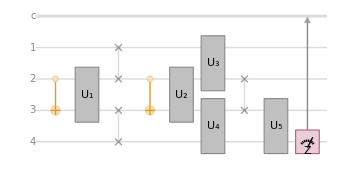

```mathematica
circuitPlot[gates, 5]
```

```mathematica
Module[{inputState,ψ, qc},
qc=quantumCircuit[gates, 5];
inputState=#;
ψ={{-Graphics-, QuantumState}}[tensor@@b2v/@inputState];
Values[qc[ψ]["Probabilities"]]//v2b
]&/@{{0, 0}, {0, 1}, {1, 0}, {1, 1}}
```

{0,1,1,0}

```mathematica
n-
```